```mathematica
p0[a_]:=Exp[-a^2];
pSucc[a_,b_]:=(p0[a+b]+1-p0[-a+b])/2;
pHom[a_]:=(1+Erf[Sqrt[2]*a])/2;
pKenOp[a_]:=NMaximize[pSucc[a,b],{b}];
pHel[a_]:=(1+Sqrt[1-Exp[-4a^2]])/2;
```

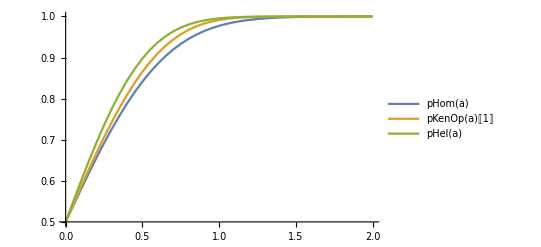

```mathematica
DiscretePlot[{pHom[a],pKenOp[a][[1]],pHel[a]},{a,0.,2.,.05},Filling->None,Joined->True,PlotLegends->"Expressions"]
```

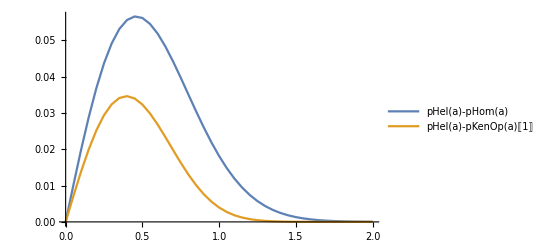

```mathematica
DiscretePlot[{pHel[a]-pHom[a],pHel[a]-pKenOp[a][[1]]},{a,0.,2.,.05},Filling->None,Joined->True,PlotLegends->"Expressions"]
```